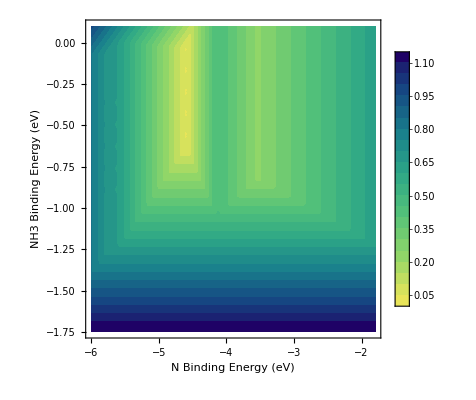

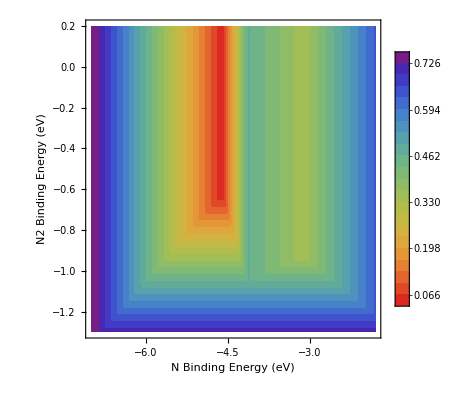

```mathematica
entropyh2o=0.2168394069;
entropyno2=0.77070379658;
Eh=0.2267*En-1.6265;
Eo=0.5892*En-2.1298;
Enh=0.7259*En-0.637;
Enh2=0.3415*En-0.7137;
Eno=0.6626*En+1.1901;
Eno2=0.2827*En+0.06581;
En2o=0.46882*En+2.24991;
En2oh=0.38843*En+0.91176;
Enoh=0.7662*En+0.8435;
Ehno=0.5189*En+0.76457;
Eh2no=0.38302*En+0.5161;
Ehnoh=0.44823*En+0.51308;
Eh2noh=0.20764*En+0.12055;
Enatom=-3.10271;
Eoatom=-1.56764627;
Ehatom=-1.11204897;
Enhmolecule=-8.08423445;
Enh2molecule=-13.51903612;
Enh3molecule=-19.51440519;
Enomolecule=-12.28259278;
En2omolecule=-21.3798;
Eno2molecule=-18.3815;
Eohmolecule=-7.56092;
En2molecule=-16.6013;
En2ohmolecule=Eohmolecule+En2molecule;
Eh2omolecule=-14.2172;
Eh3omolecule=-15.3356;
Enohmolecule=-14.7165787;
Ehnohmolecule=-19.59124351;
Eh2nohmolecule=-24.45175763;
Ehnomolecule=-15.67357977;
Eh2nomolecule=-20.00883578;

E1barrier=(En+Eo)*0.3221+5.0136;
Eh2barrier=En*0.2267+1.0388;

E1barrier=(En+Eo)*0.3221+5.0136;

G2=Eno+Enomolecule+Eh2omolecule-Eno2-Eno2molecule-2*Eh-2*Ehatom-entropyh2o;

G3=En+Enatom+Eo+Eoatom-Eno-Enomolecule;

G4=Enh-En-Eh+Enhmolecule-Enatom-Ehatom;

G5=Enh2-Enh-Eh+Enh2molecule-Enhmolecule-Ehatom;

G6=Enh3-Enh2-Eh+Enh3molecule-Enh2molecule-Ehatom;

G7=En2o+2*Eh2omolecule-En-Eh3omolecule-Eh+En2omolecule-Enatom-Eno2molecule-Ehatom-entropyh2o+entropyno2;

G8=En2oh-En2o-Eh+En2ohmolecule-En2omolecule-Ehatom;

G9=En2+Eh2omolecule-En2oh-Eh+En2molecule-En2ohmolecule-Ehatom;

G10=Enoh+Enohmolecule-Eno-Enomolecule-Eh-Ehatom;

G11=En+Enatom+Eh2omolecule-Enoh-Enohmolecule-Eh-Ehatom-entropyh2o;

G12=Ehnoh+Ehnohmolecule-Enoh-Enohmolecule-Eh-Ehatom;

G13=Enh+Enhmolecule+Eh2omolecule-Ehnoh-Ehnohmolecule-Eh-Ehatom-entropyh2o;

G14=Eh2noh+Eh2nohmolecule-Ehnoh-Ehnohmolecule-Eh-Ehatom;

G15=Ehnoh+Ehnohmolecule-Ehno-Ehnomolecule-Eh-Ehatom;

G16=Eh2no+Eh2nomolecule-Ehno-Ehnomolecule-Eh-Ehatom;

G17=Eh2noh+Eh2nohmolecule-Eh2no-Eh2nomolecule-Eh-Ehatom;

G18=Enh2+Enh2molecule+Eh2omolecule-Eh2noh-Eh2nohmolecule-Eh-Ehatom-entropyh2o;

G19=Ehno+Ehnomolecule-Eno-Enomolecule-Eh-Ehatom;

Gn2desorption=-En2-0.59;
Gnh3desorption=-Enh3-0.59;

Gnh3formpath1=Max[Eh2barrier,G2,G3,G4,G5,G6,Gnh3desorption];
Gnh3formpath2=Max[Eh2barrier,G2,G10,G11,G4,G5,G6,Gnh3desorption];
Gnh3formpath3=Max[Eh2barrier,G2,G10,G12,G13,G5,G6,Gnh3desorption];
Gnh3formpath4=Max[Eh2barrier,G2,G10,G12,G14,G18,G6,Gnh3desorption];
Gnh3formpath5=Max[Eh2barrier,G2,G19,G16,G17,G18,G6,Gnh3desorption];
Gnh3max=Min[Gnh3formpath1,Gnh3formpath2,Gnh3formpath3,Gnh3formpath4,Gnh3formpath5];

Gn2formpath1=Max[Eh2barrier,G2,G3,G7,G8,G9,Gn2desorption];
Gn2formpath2=Max[Eh2barrier,G2,G10,G11,G8,G9,Gn2desorption];
Gn2max=Min[Gn2formpath1,Gn2formpath2];

NH3volcano=ContourPlot[Gnh3max,{En,-6,-1.8},{Enh3,-1.75,0.1},Contours->22,Exclusions->None,ColorFunction-> ColorData[{"BlueGreenYellow","Reverse"}],ContourStyle->None,PlotTheme-> "Web",FrameLabel->{Style["N Binding Energy (eV)",Large,Black],Style["NH3 Binding Energy (eV)",Large,Black]},LabelStyle->Directive[Medium,Black]]
N2volcano=ContourPlot[Gn2max,{En,-7,-1.8},{En2,-1.3,0.2},Contours->22,Exclusions->None,ColorFunction-> ColorData[{"Rainbow","Reverse"}],ContourStyle->None,PlotTheme-> "Web",FrameLabel->{Style["N Binding Energy (eV)",Large,Black],Style["N2 Binding Energy (eV)",Large,Black]},LabelStyle->Directive[Medium,Black]]
```